# Övning 2

## Visualisering

## Diagram

### Hantering av data

Datapunkter hanteras som en lista av punkter {x,y}

```mathematica
uidata = {{1.9,0.8},{2.5,1.6},{4.0,2.1}, {5.0, 2.7}, {6.5, 3.6}, {8.0, 4.2}}
```

{{1.9,0.8},{2.5,1.6},{4.,2.1},{5.,2.7},{6.5,3.6},{8.,4.2}}

För att studer ett visst element i listan kan man använda Part[] eller operatorn [[]]. För att få exempelvis tredje datapunkten i listan ovan skriver man som följande:

```mathematica
uidata [[3]]
```

{4.,2.1}

Om man istället vill studera den x-värdet för den tredje data punkten skriver man

```mathematica
uidata [[3, 1]]
```

4.

och om man vill få fram y - värdet:

```mathematica
uidata[[3,2]]
```

2.1

### Visualisering av data

Nedanstående lista beskriver hur koldioxidhalten har förändrats i mellan år 1930 och 2018

```mathematica
co2data={{1930, 297}, {1940, 306}, {1950, 314}, {1960, 319}, {1970, 326}, {1980, 339}, {1990, 354}, {2000, 369}, {2010, 389}, {2015, 400}, {2017, 405}, {2018, 408}};
```

Uppmätta data som representerar en tidsserie eller funktion kan visualiseras med ett punktdiagram som skapas med kommandot ListPlot.

```mathematica
?ManipulateList
```

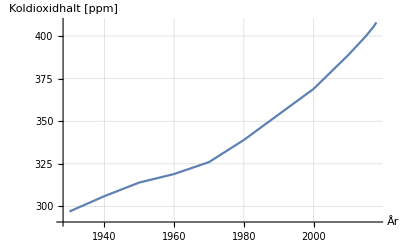

```mathematica
ListLinePlot [co2data, AxesLabel -> {"År", "Koldioxidhalt [ppm]"}, PlotStyle->PointSize[ 0.1], GridLines -> Automatic]
```

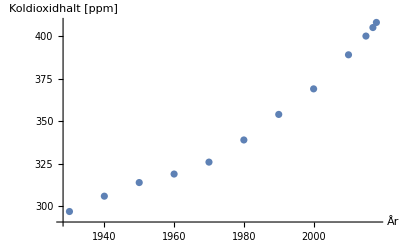

```mathematica
p1=ListPlot[co2data, AxesLabel -> {"År", "Koldioxidhalt [ppm]"}]
```

### Kurvanpassning

Man kan anpassa en modell till datapunkter med hjälp av funktionen FindFit. Här är ett försök till att anpassa en linjär modell till CO2 datat i föregående exempel

```mathematica
FindFit::usage
```

FindFit[data,expr,pars,vars] finds numerical values of the parameters pars that make expr give a best fit to data as a function of vars. 
FindFit[data,{expr,cons},pars,vars] finds a best fit subject to the parameter constraints cons.

```mathematica
{a1,b1}={a,b}/.FindFit[co2data, {a(t-1930)+b}, {a,b},t]
```

{1.27337,286.376}

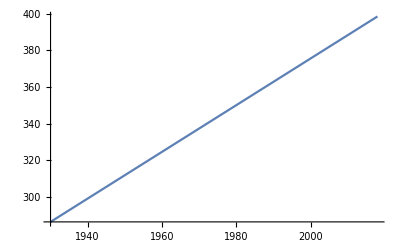

```mathematica
p2=Plot[a1(t-1930)+b1,{t,1930,2018}]
```

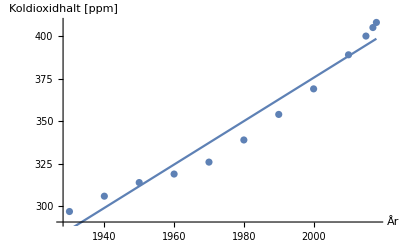

```mathematica
Show[p1,p2]
```

### Grafritning

Funktionen Plot används för att rita grafer av funktioner. Om man ska rita grafer för funktioner av två varialer kan man använda Plot3D. Plot finns också i varianter med Logaritmiska axlar:

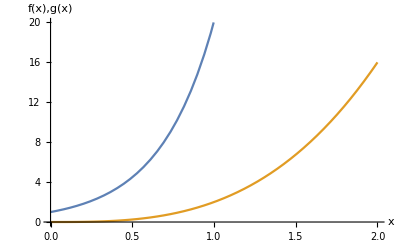

```mathematica
p1 =Plot[{Exp[3x],2x^3},{x,0,2}, PlotRange -> {{0,2},{0,20}}, AxesLabel -> {"x","f(x),g(x)"}]
```

LogPlot::prng: Value of option PlotRange -> {{0,2 AxesLabel},{0.1 AxesLabel,20 AxesLabel}}→{x,f(x),g(x)} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

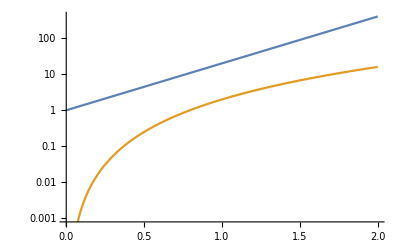

```mathematica
p2=LogPlot[{Exp[3x],2x^3},{x,0,2}, PlotRange ->{{0,2},{0.1,20}} AxesLabel ->{"x","f(x),g(x)"}]
```

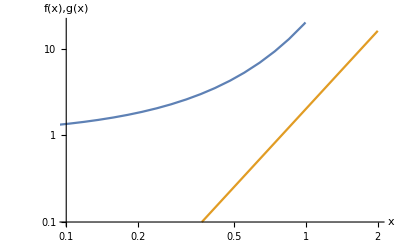

```mathematica
p3=LogLogPlot[{Exp[3x],2x^3},{x,0,2},PlotRange-> {{0.1,2},{0.1,20}}, AxesLabel -> {"x","f(x),g(x)"}]
```

```mathematica
p4=Plot3D[Cos[2x]Sin[3y], {x, 0, Pi}, {y,0, Pi}, AxesLabel->{"x", "y", "z"}]
```

-Graphics3D-

### Diagram och visualisering av information

Stapeldiagram används när data är kategoriserad i olika diskreta grupper. Höjden på stapeldiagrammet anger värdet för just den diskreta gruppen. Det finns inget funktionsvärde på x-axeln, bara en beteckning på dem diskreta gruppen. Livslön för olika yrkesgrupper är följande:

ChartLabels→Placed[{aaa,bbb,ccc},Center,#1&]

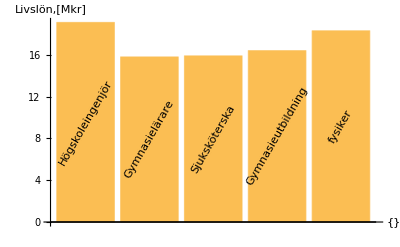

```mathematica
ll={19.1,15.8,15.9,16.4,18.3};
llLabel={"Högskoleingenjör","Gymnasielärare","Sjuksköterska","Gymnasieutbildning","fysiker"};
ChartLabels -> Placed[{"aaa","bbb","ccc"},Center,Rotate[#, 45 Degree]&]
BarChart[ll,ChartLabels->Placed[llLabel,Center,Rotate[#,60Degree] &], AxesLabel-> {{},"Livslön,[Mkr]"}]
```